Phase plot of the unscaled equations

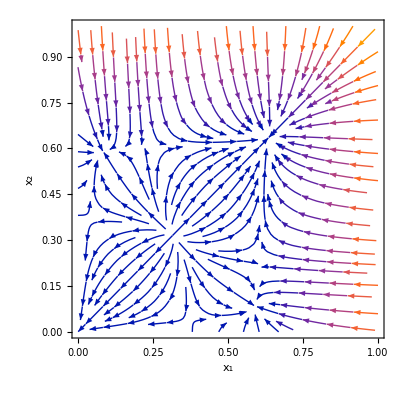

```mathematica
k = 20;
q=20;
Subscript[ϵ, 2]=0.5k;
Subscript[ϵ, 3]=0.95q;
γ=2;
Subscript[β, 2]=0.2γ/k;
Subscript[β, 3]=4γ/k;
StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2]/2(1-Subscript[x, 1])(k(Subscript[x, 1]+Subscript[x, 2])+Subscript[ϵ, 2](Subscript[x, 1]-Subscript[x, 2]))+Subscript[β, 3]/4(1-Subscript[x, 1])(q (Subscript[x, 1]+Subscript[x, 2])^2+Subscript[ϵ, 3](3 Subscript[x, 1]^2-2 Subscript[x, 1] Subscript[x, 2]-Subscript[x, 2]^2)),-γ Subscript[x, 2]+Subscript[β, 2]/2(1-Subscript[x, 2])(k(Subscript[x, 1]+Subscript[x, 2])+Subscript[ϵ, 2](Subscript[x, 2]-Subscript[x, 1]))+Subscript[β, 3]/4(1-Subscript[x, 2])(q (Subscript[x, 1]+Subscript[x, 2])^2+Subscript[ϵ, 3](3 Subscript[x, 2]^2-2 Subscript[x, 1] Subscript[x, 2]-Subscript[x, 1]^2))},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,16], PlotRange->{{0,1},{0,1}}]
```

Phase plot of the rescaled equations

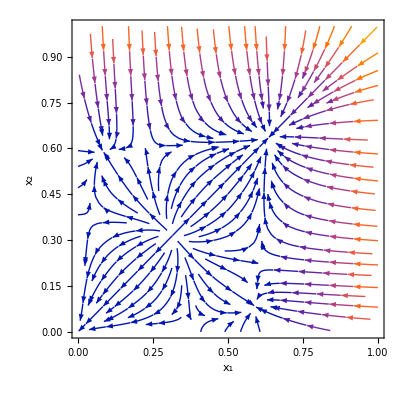

```mathematica
Subscript[ϵ, 2]=0.5;
Subscript[ϵ, 3]=0.95;
Subscript[β, 2]=0.2;
Subscript[β, 3]=4;
StreamPlot[{-Subscript[x, 1]+Subscript[β, 2]/2(1-Subscript[x, 1])((Subscript[x, 1]+Subscript[x, 2])+Subscript[ϵ, 2](Subscript[x, 1]-Subscript[x, 2]))+Subscript[β, 3]/4(1-Subscript[x, 1])((Subscript[x, 1]+Subscript[x, 2])^2+Subscript[ϵ, 3](3 Subscript[x, 1]^2-2 Subscript[x, 1] Subscript[x, 2]-Subscript[x, 2]^2)),- Subscript[x, 2]+Subscript[β, 2]/2(1-Subscript[x, 2])((Subscript[x, 1]+Subscript[x, 2])+Subscript[ϵ, 2](Subscript[x, 2]-Subscript[x, 1]))+Subscript[β, 3]/4(1-Subscript[x, 2])((Subscript[x, 1]+Subscript[x, 2])^2+Subscript[ϵ, 3](3 Subscript[x, 2]^2-2 Subscript[x, 1] Subscript[x, 2]-Subscript[x, 1]^2))},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,16], PlotRange->{{0,1},{0,1}}]
```

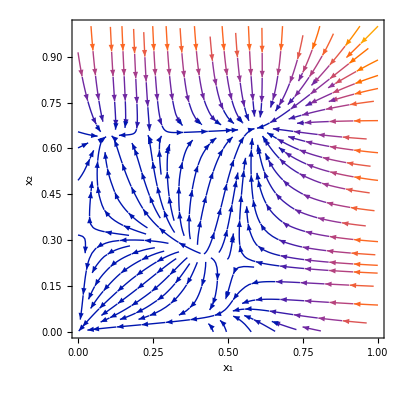

```mathematica
k=20;
q=20;
Subscript[ϵ, 2]=10;
Subscript[ϵ, 3]=19;
ρ=0.485;
γ=1;
Subscript[β, 2]=0.01;
Subscript[β, 3]=0.2;
Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2](1-Subscript[x, 1])(ρ(k+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(k-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3](1-Subscript[x, 1])(ρ^2(q+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+(1-ρ)^2(q-Subscript[ϵ, 3])(2 Subscript[x, 1] Subscript[x, 2]+Subscript[x, 2]^2)),-γ Subscript[x, 2]+Subscript[β, 2](1-Subscript[x, 2])((1-ρ)(k+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(k-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3](1-Subscript[x, 2])((1-ρ)^2(q+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+ρ^2(q-Subscript[ϵ, 3])(2 Subscript[x, 2] Subscript[x, 1]+Subscript[x, 1]^2))},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,16], PlotRange->{{0,1},{0,1}}]
```

```mathematica
Manipulate[Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2](1-Subscript[x, 1])(ρ(k+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(k-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3](1-Subscript[x, 1])(ρ^2(q+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+(1-ρ)^2(q-Subscript[ϵ, 3])(2 Subscript[x, 1] Subscript[x, 2]+Subscript[x, 2]^2)),-γ Subscript[x, 2]+Subscript[β, 2](1-Subscript[x, 2])((1-ρ)(k+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(k-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3](1-Subscript[x, 2])((1-ρ)^2(q+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+ρ^2(q-Subscript[ϵ, 3])(2 Subscript[x, 2] Subscript[x, 1]+Subscript[x, 1]^2))},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,16], PlotRange->{{0,1},{0,1}}],{ρ,0.3,0.5,0.01}]
```

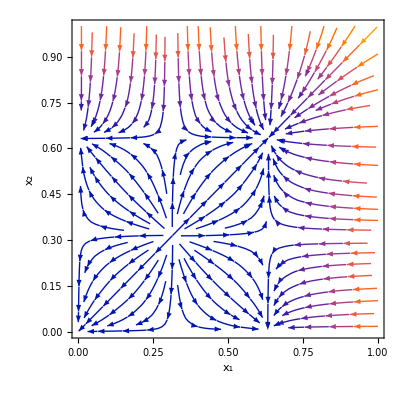

```mathematica
k=20;
q=20;
Subscript[ϵ, 2]=18;
Subscript[ϵ, 3]=20;
ρ=0.5;
γ=1;
b2crit =γ/k;
b3crit =γ/q;
Subscript[β, 2]=0.2b2crit;
Subscript[β, 3]=4b3crit;
Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2](1-Subscript[x, 1])((ρ^2+(1-ρ)^2)(k+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(k-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3](1-Subscript[x, 1])((ρ^3+(1-ρ)^3)(q+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+(1-ρ)^2(q-Subscript[ϵ, 3])(2 Subscript[x, 1] Subscript[x, 2]+Subscript[x, 2]^2)),-γ Subscript[x, 2]+Subscript[β, 2](1-Subscript[x, 2])((ρ^2+(1-ρ)^2)(k+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(k-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3](1-Subscript[x, 2])((ρ^3+(1-ρ)^3)(q+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+ρ^2(q-Subscript[ϵ, 3])(2 Subscript[x, 2] Subscript[x, 1]+Subscript[x, 1]^2))},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,16], PlotRange->{{0,1},{0,1}}]
```

```mathematica
Manipulate[Subscript[r, 2]=(1-ρ^2-(1-ρ)^2)/(ρ^2+(1-ρ)^2);
Subscript[r, 3]=(1-ρ^3-(1-ρ)^3)/(ρ^3+(1-ρ)^3);
StreamPlot[{-γ Subscript[x, 1]+Subscript[β, 2](1-Subscript[x, 1])((ρ^2+(1-ρ)^2)(k+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 1]+(1-ρ)(k-Subscript[ϵ, 2])Subscript[x, 2])+Subscript[β, 3](1-Subscript[x, 1])((ρ^3+(1-ρ)^3)(q+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 1]^2+(1-ρ)^2(q-Subscript[ϵ, 3])(2 Subscript[x, 1] Subscript[x, 2]+Subscript[x, 2]^2)),-γ Subscript[x, 2]+Subscript[β, 2](1-Subscript[x, 2])((ρ^2+(1-ρ)^2)(k+Subscript[r, 2] Subscript[ϵ, 2])Subscript[x, 2]+ρ(k-Subscript[ϵ, 2])Subscript[x, 1])+Subscript[β, 3](1-Subscript[x, 2])((ρ^3+(1-ρ)^3)(q+Subscript[r, 3] Subscript[ϵ, 3])Subscript[x, 2]^2+ρ^2(q-Subscript[ϵ, 3])(2 Subscript[x, 2] Subscript[x, 1]+Subscript[x, 1]^2))},{Subscript[x, 1],0,1},{Subscript[x, 2],0,1},Axes->True,FrameLabel->{"x_1","x_2"},LabelStyle->Directive[Black,Bold,16], PlotRange->{{0,1},{0,1}}],{ρ,0,0.5}]
```